## Exploración del parámetro gamma

```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β,Γ]
```

```mathematica
β = 0.3; Ω = 0.5;Γ=0.2
```

0.2

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10]
```

{InterpolatingFunction[{{-250., 250.}}, <>],InterpolatingFunction[{{-250., 250.}}, <>],InterpolatingFunction[{{-250., 250.}}, <>]}

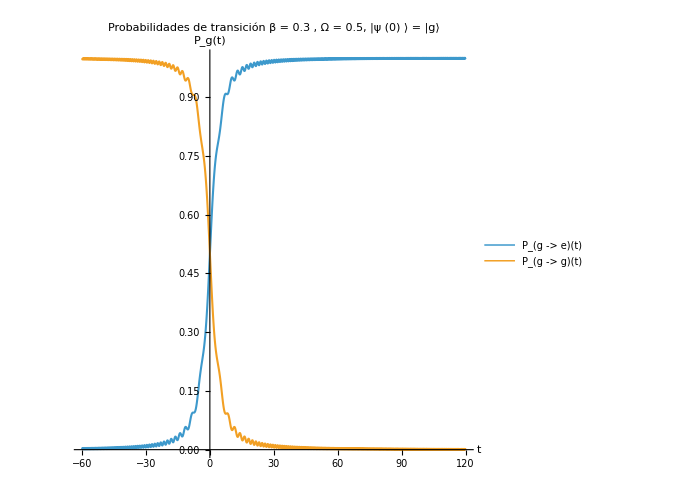

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2}, {t, -60, 120}, PlotLegends-> {"P_(g -> e)(t)", "P_(g -> g)(t)"},
PlotLabel->Style["Probabilidades de transición  β = 0.3 , Ω = 0.5, |ψ (0) ⟩ = |g⟩ ", 16, FontFamily->"Times New Roman", Black],
AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500, PlotStyle->Thickness[0.003]]
```

### Estado base inicial

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S1[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
G2 =ListLinePlot[ParallelTable[{ω,S1[Γ,ω,3.6,-200]},{ω,-3.2,3.2,0.025}],PlotRange->{-0.05,4.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=3.6",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 ) ⟩ = | g ⟩ \n β = 0.3, Ω = 0.5, Γ = 0.2, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

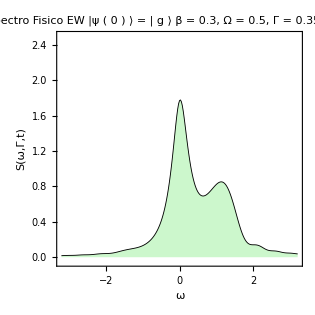
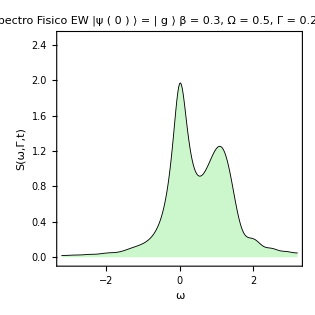
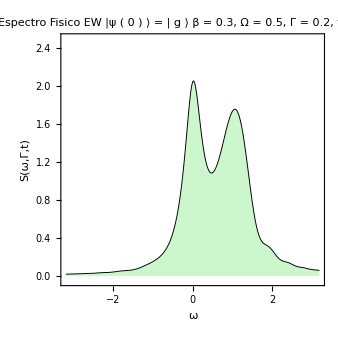
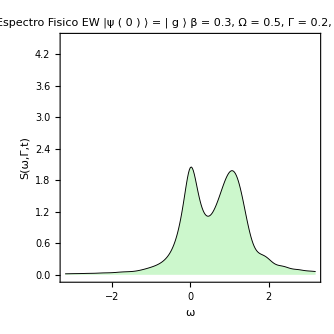
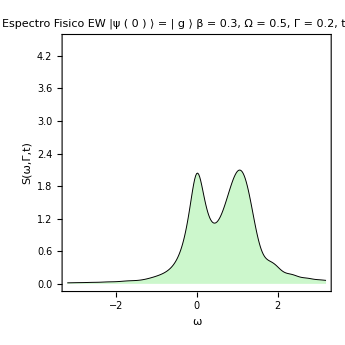
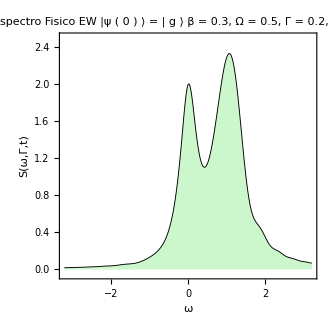
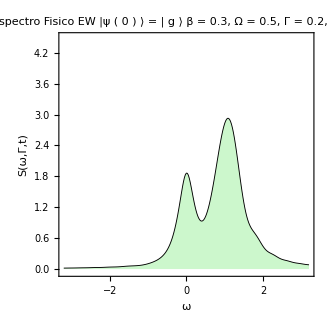

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/imagenes2/Gamma02/beta03_omega05/t=-5.png",G2,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/imagenes2/Gamma02/beta03_omega05/t=-5.png

```mathematica
"/home/roberto/Documents/SS_OptCuantica/imagenes2/Gamma02/beta03_omega02/t=-3.png"
```

/home/roberto/Documents/SS_OptCuantica/imagenes2/Gamma02/beta03_omega02/t=-3.png

### Estado excitado inicial

```mathematica
L1[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
L2[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S2[Γ_,ω_,T_,T0_]:=2Γ Exp[-2Γ T](L1[Γ,ω,T,T0]+L2[Γ,ω,T,T0])
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

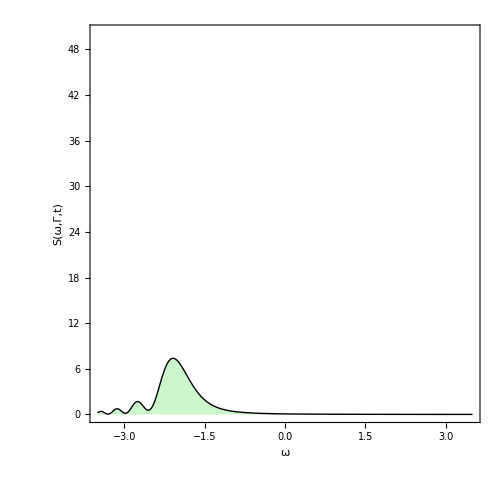

```mathematica
G1 =ListLinePlot[ParallelTable[{ω,S2[0.1,ω,-20,-200]},{ω,-3.5,3.5,0.025}],PlotRange->{-0.05,50.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/Screenshots/Lineal/b=01_0=025/zoom_omega_excitado2/t=52.png",G1,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/Screenshots/Lineal/b=01_0=025/zoom_omega_excitado2/t=52.png

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.99384×10^-7+0.0000400718 ⅈ and 4.61231×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000237749-0.0000234867 ⅈ and 4.65487×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

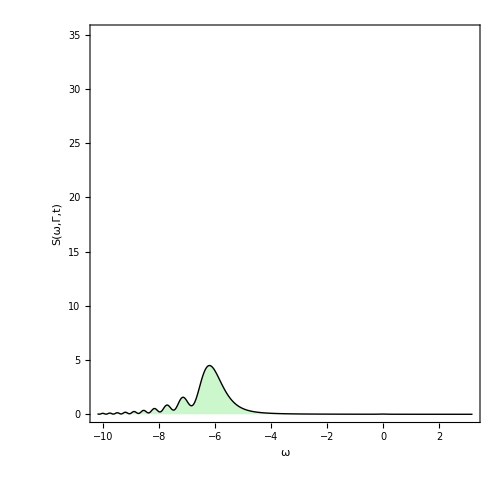

```mathematica
G2 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,-30,-200]},{ω,-10.2,3.2,0.025}],PlotRange->{-0.05,25.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-30",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```